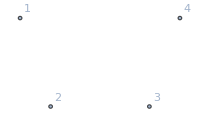
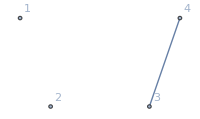
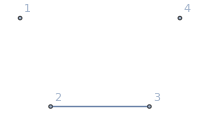
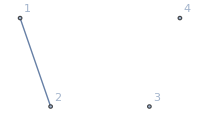
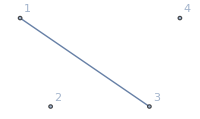
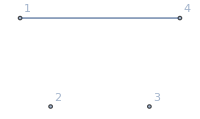
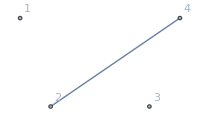
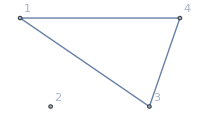
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
With[
{id=InverseReplacements[key]},
Graph[VertexDelete[newAssoc[id]["graph"],5],ImageSize->200]//Framed
]
,{key,Keys[InverseReplacements]}
]//DeleteDuplicates
```

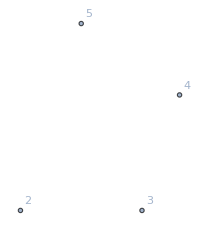
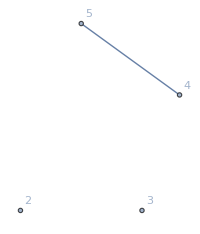
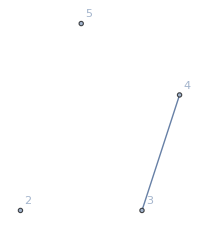
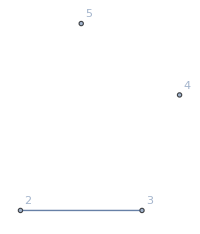
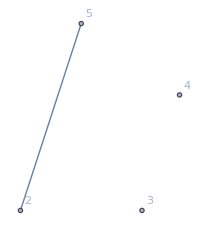
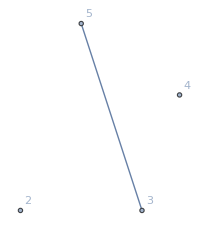
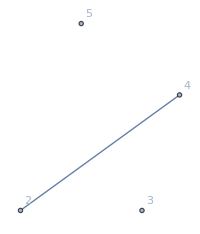
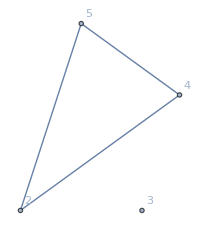
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
With[
{id=InverseReplacements[key]},
Graph[VertexDelete[newAssoc[id]["graph"],1],ImageSize->200]//Framed
]
,{key,Keys[InverseReplacements]}
]//DeleteDuplicates
```

```mathematica
Out[301]//Length
```

16

```mathematica
-Graphics-==-Graphics-
```

True

```mathematica
Normalize[x+y==z]
```

(x+y==z)/Norm[x+y==z]